```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY182_cloudy/sec_int_data/368nm.dat"]
```

{{1.83648,-1.08173},{1.67469,-0.953474},{1.55096,-0.918719},{1.77833,-1.01921},{1.08395,-0.492986},{1.0884,0.871879},{1.10777,-0.609174},{1.1184,-0.563928},{1.90886,-1.13286}}

1.14294-1.23112 x

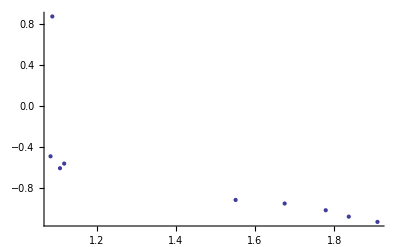

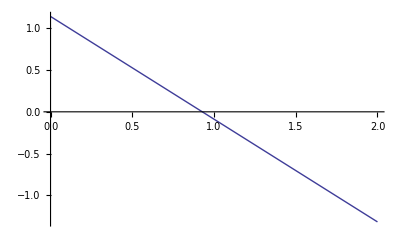

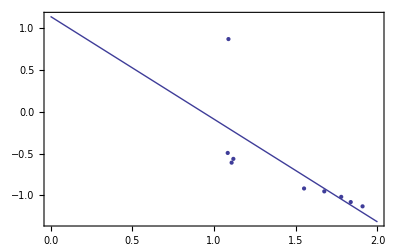

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```